## Looking what remains if we put all constraints on the solutions

Firs we take the graph

```mathematica
g=Graph[EdgeList[EdgeAdd[WheelGraph[6,VertexLabels->"Name"],{2 <->7,3 <->7,3 <->8,4 <->8,7 <->8}]],GraphLayout->"SpringEmbedding",VertexLabels->"Name"];
```

From this graph we remove 3 edges to see what the remaining solutions are

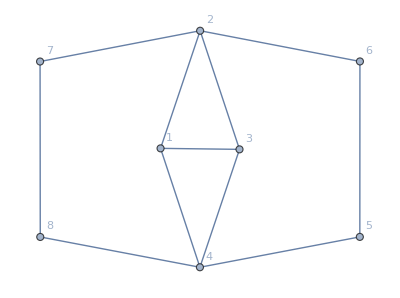

```mathematica
h=EdgeDelete[g,{3<->7,3<->8,1<->6,1<->5}]
```

```mathematica
solutions2=Select[FindFullFormula[h],SymbolLevel[#]==4&]
```

{v1x2x358x467,v1x28x35x467,v1x28x357x46,v1x258x3x467,v1x25x38x467,v1x258x37x46,v1x258x367x4,v1x25x368x47,v1x258x36x47,v1x24x367x58,v1x24x368x57,v1x24x357x68,v1x24x358x67,v18x2x35x467,v18x2x357x46,v18x25x3x467,v18x25x37x46,v18x25x367x4,v18x25x36x47,v18x24x367x5,v18x24x36x57,v18x24x357x6,v18x24x35x67,v17x2x358x46,v17x28x35x46,v17x258x3x46,v17x25x38x46,v17x25x368x4,v17x258x36x4,v17x24x368x5,v17x24x36x58,v17x24x358x6,v17x24x35x68,v168x2x357x4,v167x2x358x4,v16x2x358x47,v168x2x35x47,v16x28x357x4,v167x28x35x4,v16x28x35x47,v167x258x3x4,v16x258x3x47,v168x25x3x47,v167x25x38x4,v16x25x38x47,v16x258x37x4,v168x25x37x4,v167x24x3x58,v168x24x3x57,v167x24x38x5,v16x24x38x57,v168x24x37x5,v16x24x37x58,v16x24x358x7,v168x24x35x7,v16x24x357x8,v167x24x35x8,v158x2x3x467,v15x2x38x467,v157x2x38x46,v158x2x37x46,v158x2x367x4,v157x2x368x4,v15x2x368x47,v158x2x36x47,v15x28x3x467,v157x28x3x46,v15x28x37x46,v15x28x367x4,v157x28x36x4,v15x28x36x47,v157x24x3x68,v158x24x3x67,v157x24x38x6,v15x24x38x67,v158x24x37x6,v15x24x37x68,v15x24x368x7,v158x24x36x7,v15x24x367x8,v157x24x36x8}

```mathematica
Length[solutions2]
```

81

```mathematica
SymbolToColoring2[s_]:=Block[{sets=SymbolToSets[s],result={},colors={Red,Blue,Yellow,Green,Orange },colorpos=1},
Table[
Table[
AppendTo[result,v->Framed[v,FrameStyle->colors[[colorpos]]]]
,{v,block}
];
colorpos++;
If[colorpos>Length[colors],colorpos=1];
,{block,sets}
];
result
]
```

```mathematica
RightHasPattern[s_]:=PartitionHasPattern[SymbolToSets[s],{{2},{3,5},{4,6}}]||
PartitionHasPattern[SymbolToSets[s],{{3},{2,5},{4,6}}]||
PartitionHasPattern[SymbolToSets[s],{{4},{3,6},{2,5}}]||
PartitionHasPattern[SymbolToSets[s],{{5},{2,4},{3,6}}]||
PartitionHasPattern[SymbolToSets[s],{{6},{2,4},{3,5}}]
```

```mathematica
LeftHasPattern[s_]:=PartitionHasPattern[SymbolToSets[s],{{1},{2,8},{4,7}}]||
PartitionHasPattern[SymbolToSets[s],{{2},{1,8},{4,7}}]||
PartitionHasPattern[SymbolToSets[s],{{4},{1,7},{2,8}}]||
PartitionHasPattern[SymbolToSets[s],{{7},{2,4},{1,8}}]||
PartitionHasPattern[SymbolToSets[s],{{8},{2,4},{1,7}}]
```

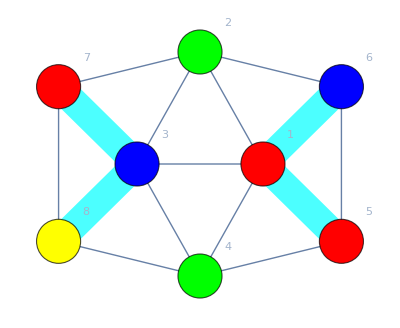
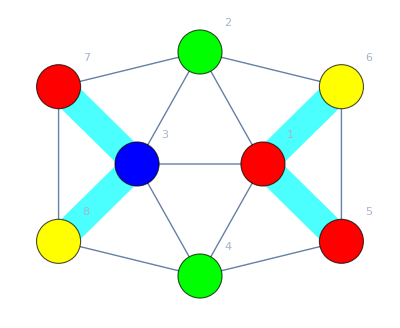
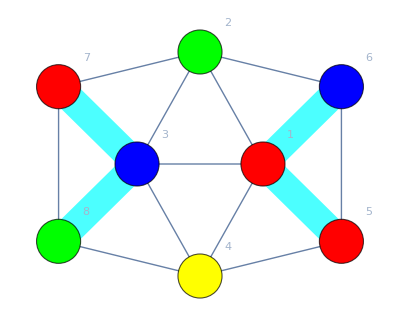
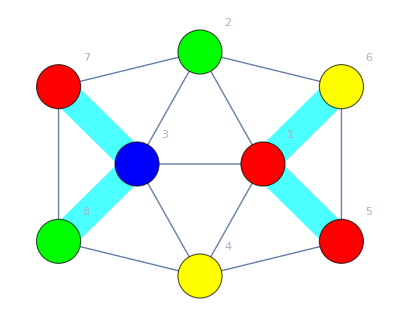
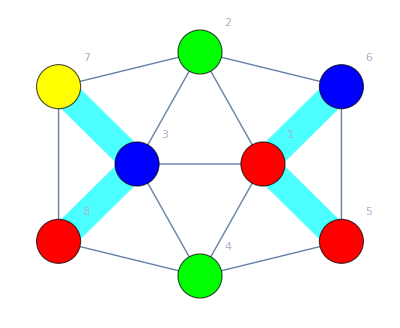
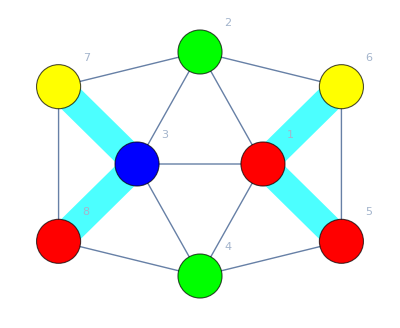
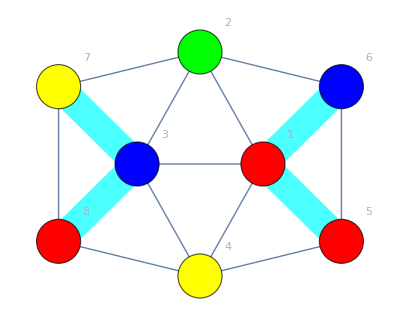
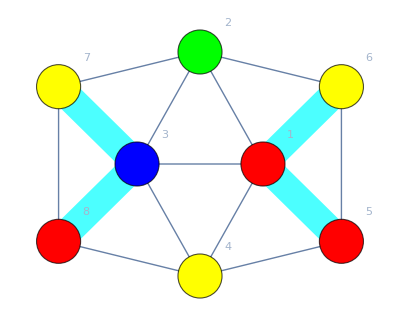
{3,7,True,v157x24x36x8,157♁24♁36♁8,-Graphics-,12345678,3!=7,3!=8,1!=6,1==5,True,True}
{3,7,True,v157x24x3x68,157♁24♁3♁68,-Graphics-,12345678,3!=7,3!=8,1!=6,1==5,True,False}
{3,7,True,v157x28x36x4,157♁28♁36♁4,-Graphics-,12345678,3!=7,3!=8,1!=6,1==5,True,False}
{3,7,True,v157x28x3x46,157♁28♁3♁46,-Graphics-,12345678,3!=7,3!=8,1!=6,1==5,True,False}
{3,7,True,v158x24x36x7,158♁24♁36♁7,-Graphics-,12345678,3!=7,3!=8,1!=6,1==5,True,True}
{3,7,True,v158x24x3x67,158♁24♁3♁67,-Graphics-,12345678,3!=7,3!=8,1!=6,1==5,True,False}
{3,7,True,v158x2x36x47,158♁2♁36♁47,-Graphics-,12345678,3!=7,3!=8,1!=6,1==5,True,False}
{3,7,True,v158x2x3x467,158♁2♁3♁467,-Graphics-,12345678,3!=7,3!=8,1!=6,1==5,True,False}
{3,7,True,v15x28x36x47,15♁28♁36♁47,-Graphics-,12345678,3!=7,3!=8,1!=6,1==5,True,False}
{3,7,True,v15x28x3x467,15♁28♁3♁467,-Graphics-,12345678,3!=7,3!=8,1!=6,1==5,True,False}
{3,11,True,v167x24x35x8,167♁24♁35♁8,-Graphics-,12345678,3!=7,3!=8,1==6,1!=5,True,True}
{3,11,True,v167x24x3x58,167♁24♁3♁58,-Graphics-,12345678,3!=7,3!=8,1==6,1!=5,True,False}
{3,11,True,v167x258x3x4,167♁258♁3♁4,-Graphics-,12345678,3!=7,3!=8,1==6,1!=5,True,False}
{3,11,True,v167x28x35x4,167♁28♁35♁4,-Graphics-,12345678,3!=7,3!=8,1==6,1!=5,True,False}
{3,11,True,v168x24x35x7,168♁24♁35♁7,-Graphics-,12345678,3!=7,3!=8,1==6,1!=5,True,True}
{3,11,True,v168x24x3x57,168♁24♁3♁57,-Graphics-,12345678,3!=7,3!=8,1==6,1!=5,True,False}
{3,11,True,v168x25x3x47,168♁25♁3♁47,-Graphics-,12345678,3!=7,3!=8,1==6,1!=5,True,False}
{3,11,True,v168x2x35x47,168♁2♁35♁47,-Graphics-,12345678,3!=7,3!=8,1==6,1!=5,True,False}
{3,11,True,v16x258x3x47,16♁258♁3♁47,-Graphics-,12345678,3!=7,3!=8,1==6,1!=5,True,False}
{3,11,True,v16x28x35x47,16♁28♁35♁47,-Graphics-,12345678,3!=7,3!=8,1==6,1!=5,True,False}
{3,13,True,v17x24x358x6,17♁24♁358♁6,-Graphics-,12345678,3!=7,3==8,1!=6,1!=5,True,True}
{3,13,True,v17x24x368x5,17♁24♁368♁5,-Graphics-,12345678,3!=7,3==8,1!=6,1!=5,True,True}
{3,13,True,v17x25x368x4,17♁25♁368♁4,-Graphics-,12345678,3!=7,3==8,1!=6,1!=5,False,True}
{3,13,True,v17x25x38x46,17♁25♁38♁46,-Graphics-,12345678,3!=7,3==8,1!=6,1!=5,False,True}
{3,13,True,v17x2x358x46,17♁2♁358♁46,-Graphics-,12345678,3!=7,3==8,1!=6,1!=5,False,True}
{3,13,True,v1x24x358x67,1♁24♁358♁67,-Graphics-,12345678,3!=7,3==8,1!=6,1!=5,False,True}
{3,13,True,v1x24x368x57,1♁24♁368♁57,-Graphics-,12345678,3!=7,3==8,1!=6,1!=5,False,True}
{3,13,True,v1x25x368x47,1♁25♁368♁47,-Graphics-,12345678,3!=7,3==8,1!=6,1!=5,False,True}
{3,13,True,v1x25x38x467,1♁25♁38♁467,-Graphics-,12345678,3!=7,3==8,1!=6,1!=5,False,True}
{3,13,True,v1x2x358x467,1♁2♁358♁467,-Graphics-,12345678,3!=7,3==8,1!=6,1!=5,False,True}
{3,14,True,v18x24x357x6,18♁24♁357♁6,-Graphics-,12345678,3==7,3!=8,1!=6,1!=5,True,True}
{3,14,True,v18x24x367x5,18♁24♁367♁5,-Graphics-,12345678,3==7,3!=8,1!=6,1!=5,True,True}
{3,14,True,v18x25x367x4,18♁25♁367♁4,-Graphics-,12345678,3==7,3!=8,1!=6,1!=5,False,True}
{3,14,True,v18x25x37x46,18♁25♁37♁46,-Graphics-,12345678,3==7,3!=8,1!=6,1!=5,False,True}
{3,14,True,v18x2x357x46,18♁2♁357♁46,-Graphics-,12345678,3==7,3!=8,1!=6,1!=5,False,True}
{3,14,True,v1x24x357x68,1♁24♁357♁68,-Graphics-,12345678,3==7,3!=8,1!=6,1!=5,False,True}
{3,14,True,v1x24x367x58,1♁24♁367♁58,-Graphics-,12345678,3==7,3!=8,1!=6,1!=5,False,True}
{3,14,True,v1x258x367x4,1♁258♁367♁4,-Graphics-,12345678,3==7,3!=8,1!=6,1!=5,False,True}
{3,14,True,v1x258x37x46,1♁258♁37♁46,-Graphics-,12345678,3==7,3!=8,1!=6,1!=5,False,True}
{3,14,True,v1x28x357x46,1♁28♁357♁46,-Graphics-,12345678,3==7,3!=8,1!=6,1!=5,False,True}

```mathematica
TableForm[Select[Map[With[{d=FromDigits[Reverse[{
BoolToInt[!Right1[#]],
BoolToInt[!Right2[#]],
BoolToInt[!Left1[#]],
BoolToInt[!Left2[#]]
}],2]},{Total[IntegerDigits[d,2]],d,
LeftHasPattern[#] ||
RightHasPattern[#],
#,
SymbolToLabel[#],
Graph[ColorGraph[g,SymbolToSets[#]],EdgeStyle->Map[#->Directive[Thickness[0.05],Cyan]&,{3<->7,3<->8,1<->6,1<->5}]],
Row[(Range[8]/.SymbolToColoring2[#])],
If[Right1[#],"3==7",Style["3!=7",Red]],
If[Right2[#],"3==8",Style["3!=8",Red]],
If[Left1[#],"1==6",Style["1!=6",Red]],
If[Left2[#],"1==5",Style["1!=5",Red]],
LeftHasPattern[#],
RightHasPattern[#]
}]&,Sort[solutions2,CompareSymbols]
]//Sort,#[[1]]==3&&#[[3]]==True&], TableSpacing->{1, 10}, TableDepth->1]
```

```mathematica
Map[SetsToSymbol,FindFiner [SymbolToSets[v157x24x36x8]]]
```

{v1x24x36x57x8,v15x24x36x7x8,v17x24x36x5x8,v157x2x36x4x8,v157x24x3x6x8}

```mathematica
DeleteDuplicates[Flatten[Map[Map[SetsToSymbol,FindFiner [SymbolToSets[#]]]&,{v157x24x36x8,v167x24x35x8,v17x24x358x6,v18x24x357x6}]]]
```

{v1x24x36x57x8,v15x24x36x7x8,v17x24x36x5x8,v157x2x36x4x8,v157x24x3x6x8,v1x24x35x67x8,v16x24x35x7x8,v17x24x35x6x8,v167x2x35x4x8,v167x24x3x5x8,v1x24x358x6x7,v17x2x358x4x6,v17x24x3x58x6,v17x24x38x5x6,v1x24x357x6x8,v18x2x357x4x6,v18x24x3x57x6,v18x24x35x6x7,v18x24x37x5x6}

```mathematica
GraphForSymbols[s_]:=FormulaGraphReverse[Join[s,DeleteDuplicates[Flatten[Map[Map[SetsToSymbol,FindFiner [SymbolToSets[#]]]&,s]]]]]
```

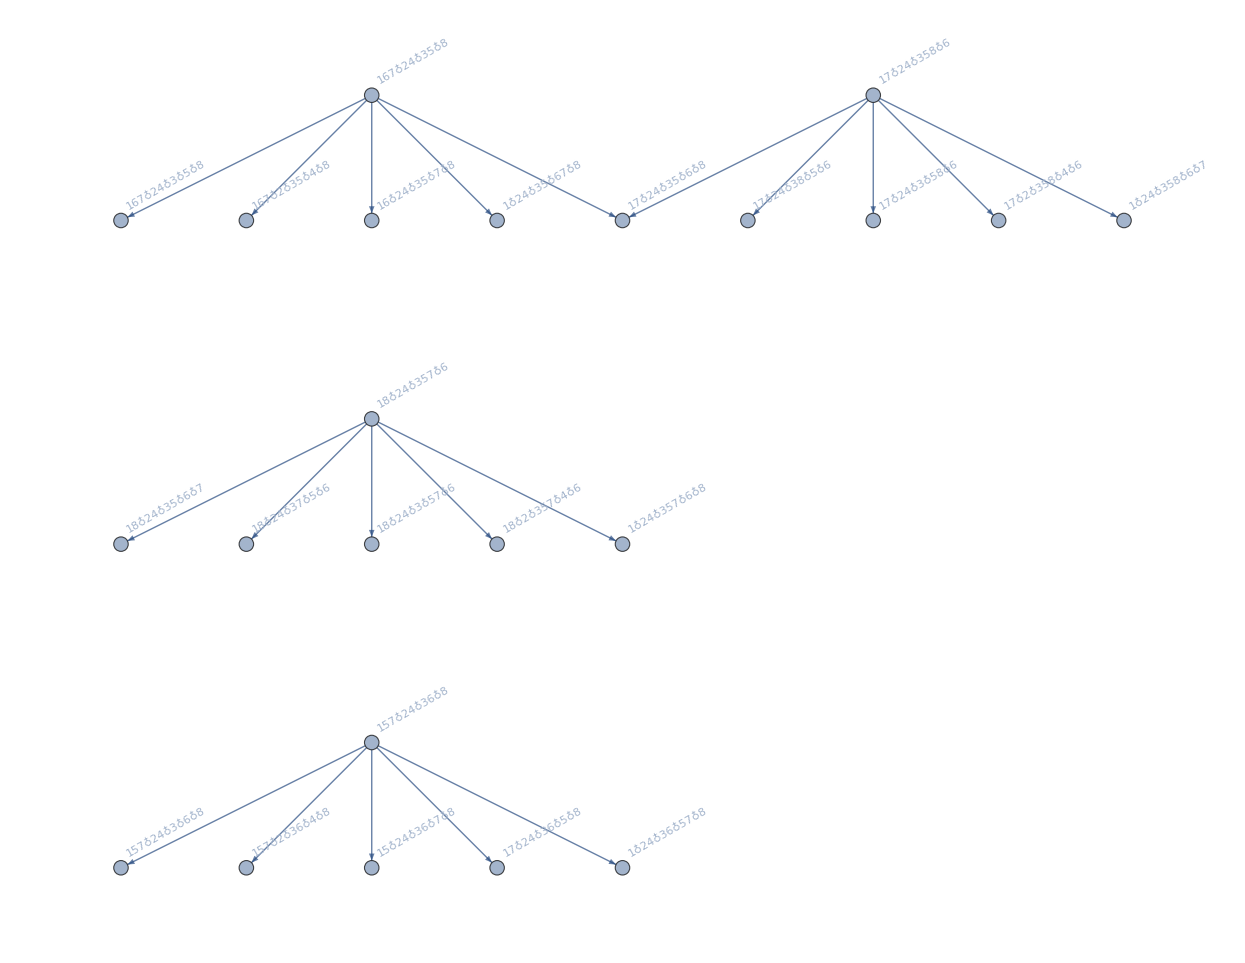

```mathematica
GraphForSymbols[{v157x24x36x8,v167x24x35x8,v17x24x358x6,v18x24x357x6}]
```